```mathematica
SetDirectory[NotebookDirectory[]];
```

# Fully coupled model

## Swept of different initial metallicity values for the fully coupled model with constant τS.

## Constants

```mathematica
τS=26/10; (*[Gyr]*)
n=404754; (*[cm^-3]*)
P=4046/100;  (*[(M_(\[PermutationProduct]))^-1 pc^3 cm^-3]*)
tot0=n/P; (*[M_(\[PermutationProduct]) pc^-3]*)
C1=303/100000000; (*[Gyr]*)
C2=874/10000000; (*[Gyr]*)
R=18/100;
ηion=95529/100;
ηdiss=38093/100;
Zsun=134/10000;
Zsn=9/100;
Zeff=Zsun*10^-3;
```

## Auxiliary function

```mathematica
gf=if[t]+af[t]+mf[t]+zf[t];
ψf=mf[t]/τS;
ifg=if[t]/gf;
afg=af[t]/gf;
mfg=mf[t]/gf;
zfg=zf[t]/gf;
τR=C1/(if[t]*tot);
τC=C2/((af[t]+mf[t])*tot)*1/(zfg+Zeff);
```

## ODE system

### Initial conditions and parameters for test run and time measurement

```mathematica
tot =tot0;
if0=1/1000;
af0=500/1000;
mf0=499/1000;
sf0=0;
Ini={if0,af0,mf0,sf0,zf0};
```

```mathematica
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### System

```mathematica
var={if[t],af[t],mf[t],sf[t],zf[t]};
equ = {
if'[t]==-if[t]/τR+(ηion+(1-Zsn)*R-ifg)*ψf,
af'[t]==-af[t]/τC+if[t]/τR+(ηdiss-ηion-afg)*ψf,
mf'[t]==af[t]/τC-(ηdiss+mfg)*ψf,
sf'[t]==(1-R)*ψf,
zf'[t]==(Zsn*R-zfg)*ψf,
if[Tstart]==if0,
af[Tstart]==af0,
mf[Tstart]==mf0,
sf[Tstart]==sf0,
zf[Tstart]==zf0
};
```

## Calculate and save solution in file

```mathematica
Zf0=Table[i,{i,0,0.03,0.0005}];
```

```mathematica
stellarF=Table[
sol=NDSolve[N[equ,60],var,{t,Tstart,Tend}][[1]];
sf[t]/.sol/.t->1,
{zf0,Zf0}]
```

{0.269343,0.269595,0.269651,0.269692,0.269727,0.26976,0.26979,0.26982,0.269848,0.269875,0.269903,0.269929,0.269955,0.269981,0.270007,0.270032,0.270057,0.270083,0.270107,0.270132,0.270157,0.270181,0.270206,0.27023,0.270255,0.270279,0.270303,0.270327,0.270351,0.270375,0.270399,0.270423,0.270447,0.270471,0.270494,0.270518,0.270542,0.270565,0.270589,0.270612,0.270636,0.270659,0.270683,0.270706,0.27073,0.270753,0.270776,0.2708,0.270823,0.270846,0.270869,0.270892,0.270916,0.270939,0.270962,0.270985,0.271008,0.271031,0.271054,0.271077,0.2711}

```mathematica
result=MapThread[{#1,#2}&,{Zf0,stellarF}];
```

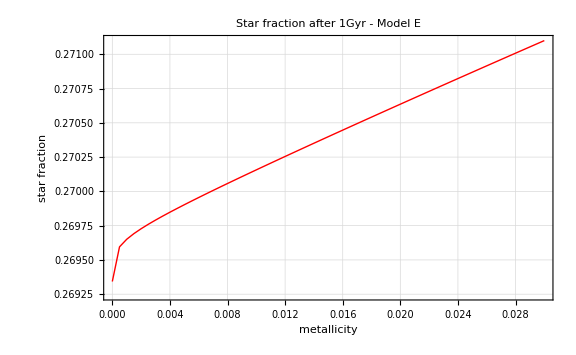

```mathematica
ListPlot[result,
Joined->True,
PlotStyle->{Thick,Red},
FrameLabel->{Style["metallicity",18],Style["star fraction",18] },
FrameStyle->Directive[Black,15],
ImageSize->Large,
Frame->True,
PlotRange->All,
GridLines->Automatic,
PlotLabel->Style["Star fraction after 1Gyr - Model E",20,Bold,Black]]
```